Evolve

Hamiltonian

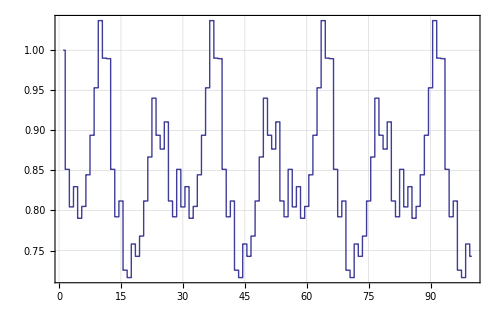

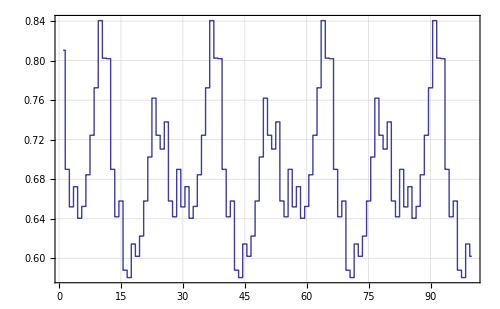

K and V

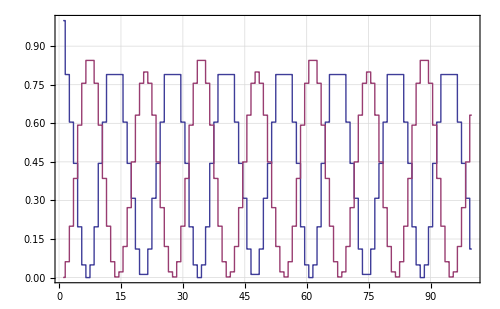

hhTbl

==========================

idxQ0 = 0, idxQ1 = 0

==========================

idxQ0 = 0, idxQ1 = 1

==========================

idxQ0 = 0, idxQ1 = 2

==========================

idxQ0 = 0, idxQ1 = 3

==========================

idxQ0 = 0, idxQ1 = 4

==========================

idxQ0 = 1, idxQ1 = 0

==========================

idxQ0 = 1, idxQ1 = 1

==========================

idxQ0 = 1, idxQ1 = 2

==========================

idxQ0 = 1, idxQ1 = 3

==========================

idxQ0 = 1, idxQ1 = 4

==========================

idxQ0 = 2, idxQ1 = 0

==========================

idxQ0 = 2, idxQ1 = 1

==========================

idxQ0 = 2, idxQ1 = 2

==========================

idxQ0 = 2, idxQ1 = 3

==========================

idxQ0 = 2, idxQ1 = 4

==========================

idxQ0 = 3, idxQ1 = 0

==========================

idxQ0 = 3, idxQ1 = 1

==========================

idxQ0 = 3, idxQ1 = 2

==========================

idxQ0 = 3, idxQ1 = 3

==========================

idxQ0 = 3, idxQ1 = 4

==========================

idxQ0 = 4, idxQ1 = 0

==========================

idxQ0 = 4, idxQ1 = 1

==========================

idxQ0 = 4, idxQ1 = 2

==========================

idxQ0 = 4, idxQ1 = 3

==========================

idxQ0 = 4, idxQ1 = 4

hhTbl = ((0
0
1/20
0
0.) | (0
1
1/20
0
0.05) | (0
2
1/20
0
0.0712549) | (0
3
1/20
0
0.115333) | (0
4
1/20
0
0.176578)
(1
0
1/20
0
0.05) | (1
1
1/20
0
0.0005) | (1
2
1/20
0
0.05) | (1
3
1/20
0
0.0631373) | (1
4
1/20
0
0.0712549)
(2
0
1/20
0
0.0701961) | (2
1
1/20
0
0.05) | (2
2
1/20
0
0.002) | (2
3
1/20
0
0.05) | (2
4
1/20
0
0.0716078)
(3
0
1/20
0
0.115804) | (3
1
1/20
0
0.0642647) | (3
2
1/20
0
0.05) | (3
3
1/20
0
0.0045) | (3
4
1/20
0
0.05)
(4
0
1/20
0
0.176931) | (4
1
1/20
0
0.0707843) | (4
2
1/20
0
0.0692843) | (4
3
1/20
0
0.05) | (4
4
1/20
0
0.008))

```mathematica
IdxQ0Max=4;
IdxQ1Max=4;

(*
useFloorVal=False;
q0Val=100;
q1Val=100;
KmHp2dMval=(1/10);
NVal=200;
*)

useFloorVal=False;
RingDivisor=10^1;
q0Val=1/RingDivisor;
q1Val=10/RingDivisor;
KmHp2dMval=(1/20);
alphaVal=(-1/2)*0;
NVal=100;

(* ============================================= *)

IMAGESIZE=500;

Qip1[qi_?NumericQ,qim1_?NumericQ,KmHp2dM_,alpha_,useFloor_?BooleanQ]:=Module[{qip1Val,qip1ExactVal},
(* Print["Qip1::Starting"]; *)
qip1ExactVal=(2-KmHp2dM)*qi-qim1-KmHp2dM*alpha;
qip1Val=If[useFloor,Floor[qip1ExactVal*RingDivisor],Round[qip1ExactVal*RingDivisor]]/RingDivisor;
(* Print["qip1Val = ", qip1Val]; *)
Return[qip1Val];
];

Evolve[q0_?NumericQ,q1_?NumericQ,KmHp2dM_,alpha_,useFloor_?BooleanQ,nStep_?IntegerQ]:=Module[{ii,qLst},
(* Print["Evolve::Starting"]; *)
qLst=Table[Indeterminate,{ii,1,nStep+2}];

qLst[[1]]=q0;
qLst[[2]]=q1;

For[ii=2,ii < nStep+2,ii++,
(
(* Print["Evolve::ii = ", ii]; *)
qLst[[ii+1]]=Qip1[qLst[[ii]],qLst[[ii-1]],KmHp2dM,alpha,useFloor];
)
];

(* Print["Evolve::qLst = ", qLst]; *)
Return[qLst];
];

KKmMdHp2[qLst_?VectorQ,KmHp2dM_,alpha_]:=Module[{len,kLst,ii},
len=Length[qLst];
kLst=Table[((qLst[[ii+1]]-qLst[[ii]])^2),{ii,1,len-1}];
Return[kLst];
];

VVmMdHp2[qLst_?VectorQ,KmHp2dM_,alpha_]:=Module[{len,vLst,ii},
len=Length[qLst];
vLst=Table[(KmHp2dM*(qLst[[ii]]+alpha)^2),{ii,1,len-1}];
Return[vLst];
];

HHmMdHp2[qLst_?VectorQ,KmHp2dM_,alpha_]:=Module[{len,hLst,ii},
len=Length[qLst];
hLst=Table[((qLst[[ii+1]]-qLst[[ii]])^2+KmHp2dM*(qLst[[ii]]+alpha)^2),{ii,1,len-1}];
Return[hLst];
];

HH0mMdHp2[qLst_?VectorQ,KmHp2dM_,alpha_]:=Module[{len,hh0},
len=Length[qLst];
hh0=((qLst[[2]]-qLst[[1]])^2+KmHp2dM*(qLst[[1]]+alpha)^2);
Return[hh0];
];

(* Function to plot vectors. *)
IndexedVariableFunc[idxVal_?NumericQ,vect_?VectorQ]:=Module[{idx,retVal,len},
len=Length[vect];
idx=Round[idxVal];
retVal=If[idx<1||idx>len,Indeterminate,vect[[idx]]];
Return[retVal];
];

BooleanQ[x_]:=If[Element[x,Booleans],True,False,False];
(* ============================================= *)

Print["Evolve"];
ql=Evolve[q0Val,q1Val,KmHp2dMval,alphaVal,useFloorVal,NVal];
hh0=HH0mMdHp2[ql,KmHp2dMval,alphaVal];
hh=HHmMdHp2[ql,KmHp2dMval,alphaVal];
kk=KKmMdHp2[ql,KmHp2dMval,alphaVal];
vv=VVmMdHp2[ql,KmHp2dMval,alphaVal];

defaultPltOpts:={PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Thick,ImageSize ->IMAGESIZE ,PlotPoints -> 2*NVal};


Print["Hamiltonian"];
Print[Plot[IndexedVariableFunc[idx,hh]/hh0,{idx,1,NVal},Evaluate[defaultPltOpts]]];
Print[Plot[IndexedVariableFunc[idx,hh],{idx,1,NVal},Evaluate[defaultPltOpts]]];

Print["K and V"];
Print[Plot[{IndexedVariableFunc[idx,kk]/hh0,IndexedVariableFunc[idx,vv]/hh0},{idx,1,NVal},Evaluate[defaultPltOpts]]];

(* ============================================= *)

Print["hhTbl"];
hhTbl=Table[Indeterminate,{idxQ0,0,IdxQ0Max},{idxQ1,0,IdxQ1Max}];

For[idxQ0=0,idxQ0 ≤ IdxQ0Max,idxQ0++,
For[idxQ1=0,idxQ1 ≤ IdxQ1Max,idxQ1++,
(
Print["=========================="];
Print["idxQ0 = ", idxQ0, ", idxQ1 = ", idxQ1];
q0Val=idxQ0/RingDivisor;
q1Val=idxQ1/RingDivisor;
ql=Evolve[q0Val,q1Val,KmHp2dMval,alphaVal,useFloorVal,NVal];
hh=HHmMdHp2[ql,KmHp2dMval,alphaVal];

(* Print[Plot[IndexedVariableFunc[idx,hh],{idx,1,NVal},Evaluate[defaultPltOpts]]]; *)

hhAvg=N[Mean[Table[hh[[ii]],{ii,Round[NVal/2],NVal}]]];

hhTbl[[idxQ0+1,idxQ1+1]]={idxQ0,idxQ1,KmHp2dMval,alphaVal,hhAvg};
)
];
];

Print["hhTbl = ", hhTbl // MatrixForm];
```